```mathematica
SetDirectory[NotebookDirectory[]]
```

## Non-idealized data

```mathematica
rawdata = Import["DataForPlotting\\Fig3B_rsMeans_data.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{3031,2}

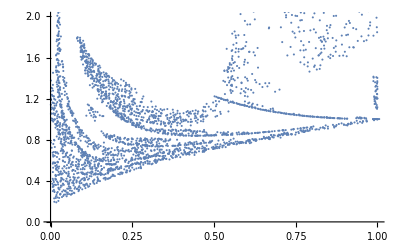

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.04}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{SetPrecision[rawdata[[n]][[1]]*10, 20],rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
SminNOISE = rescaleddata[[Position[rescaleddata[[;;,2]],Min[rescaleddata[[;;,2]]]][[1]][[1]],1]]
```

0.1766582514914286431

```mathematica
minNOISE= rescaleddata[[Position[rescaleddata[[;;,2]],Min[rescaleddata[[;;,2]]]][[1]][[1]],2]]
```

0.1904972516363982737

```mathematica
Clear[densADJ];
densADJ={{SminNOISE, minNOISE}}
```

{{0.1766582514914286431,0.1904972516363982737}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{2611,2}

```mathematica
densADJrescaled = Table[{SetPrecision[densADJ[[n]][[1]]/10,20],densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

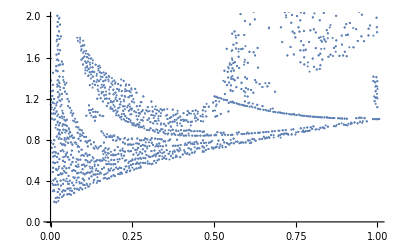

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

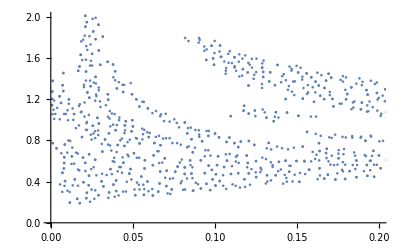

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,0.2},{0,2}}]
```

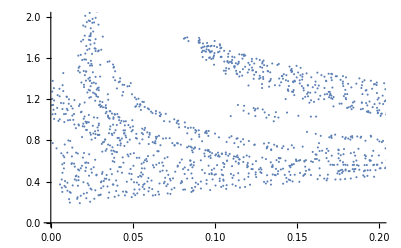

```mathematica
ListPlot[rawdata,PlotRange->{{0,0.2},{0,2}}]
```

```mathematica
Export["DataForPlotting\\Fig3B_rsMeans_densADJ.txt",densADJrescaled, "Table"]
```

## Idealized data

```mathematica
rawdata = Import["DataForPlotting\\Fig3B_data_idealized.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{745201,1}

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.1}]]<3,Prepend[x,t],x]]
```

```mathematica
geq1point8= Select[rawdata, #[[1]]>1.8 &];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[geq1point8,1]
```

{{1.97273}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rawdata],{n,1,100000}];
```

```mathematica
Dimensions[densADJ]
```

{22,1}

```mathematica
Min[rawdata]
```

1.0128

```mathematica
minNOISE= rawdata[[Position[rawdata,Min[rawdata]][[1]][[1]]]]
```

{1.0128}

```mathematica
densADJ = Join[densADJ, {minNOISE}];
```

```mathematica
densADJ[[-1]]
```

{1.0128}

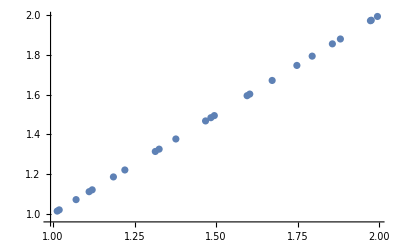

```mathematica
ListPlot[Table[{densADJ[[n]][[1]],densADJ[[n]][[1]]},{n,1,Length[densADJ]}]]
```

```mathematica
Export["DataForPlotting\\Fig3B_densADJ_idealized.txt",densADJ, "Table"]
```